```mathematica
p[x_] = Piecewise[{{x, 0 ≤ x ≤ 1/2}, {1-x, 1/2 ≤ x ≤ 1}}]
```

Piecewise[{{x, 0≤x≤1/2}, {1-x, 1/2≤x≤1}, {0, True}}]

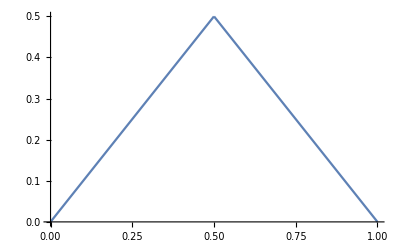

```mathematica
Plot[p[x], {x, 0, 1}]
```

```mathematica
A = Sqrt[12/a^3]
pp[x_] = Piecewise[{{A x, 0 ≤ x ≤ a/2}, {A(a-x), a/2 ≤ x ≤ a}}]
```

2 √3 √(1/a^3)

Piecewise[{{2 √3 √(1/a^3) x, 0≤x≤a/2}, {2 √3 √(1/a^3) (a-x), a/2≤x≤a}, {0, True}}]

```mathematica
Integrate[pp[x]^2, {x, 0, a}]
```

1

```mathematica
c[n_] = Sqrt[2/a]Integrate[Sin[n π x/a] pp[x], {x, 0, a}] // TrigExpand // FullSimplify
```

(8 √6 Sin[(n π)/4]^2 Sin[(n π)/2])/(n^2 π^2)

```mathematica
Sum[c[n]^2, {n, ∞}]
```

1